```mathematica
(*EE = p^2/(2 m l^2)  - m g l Cos[θ] ; *)
Solve[EE == p^2/(2 m l^2)  - m g l Cos[θ] ,p ]   //Simplify
```

{{p→-√2 √(l^2 m (EE+g l m Cos[θ]))},{p→√2 √(l^2 m (EE+g l m Cos[θ]))}}

```mathematica
Solve[EE == (0 p^2)/(2 m l^2)  - m g l Cos[θ] , θ]
```

{{θ→ConditionalExpression[-ArcCos[-EE/(g l m)]+2 π C[1], C[1]∈ℤ]},{θ→ConditionalExpression[ArcCos[-EE/(g l m)]+2 π C[1], C[1]∈ℤ]}}

```mathematica
lim = ArcCos[-EE/(g l m)] ;
g=1;l=1;m=1;
J1 = 2/(2 π)Integrate[√2 √(l^2 m (EE+g l m Cos[θ])),   {θ,-lim,lim}, Assumptions->  (*m>0&&l>0&&g>0&&*) EE>-m g l&&EE<0]
```

(4 √2 √(1+EE) EllipticE[1/4 (π+2 ArcSin[EE]),2/(1+EE)])/π

```mathematica
J2 = 2/(2 π)Integrate[√2 √(l^2 m (EE+g l m Cos[θ])),   {θ,-lim,lim}, Assumptions->  (*m>0&&l>0&&g>0&&*) EE>0&&EE<m g l]
```

(4 √2 √(1+EE) EllipticE[1/4 (3 π+2 ⅈ Log[ⅈ EE-√(1-EE^2)]),2/(1+EE)])/π

```mathematica
J3 = 2/(2 π)Integrate[√2 √(l^2 m (EE+g l m Cos[θ])),   {θ,-π,π}, Assumptions->  (*m>0&&l>0&&g>0&&*) EE>m g l]
```

(4 √2 √(-1+EE) EllipticE[-2/(-1+EE)])/π

```mathematica
Speak["Job done"]
```

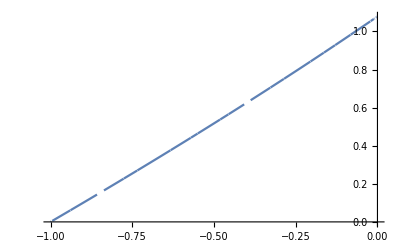

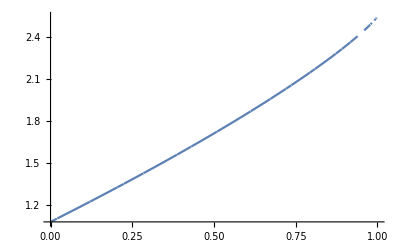

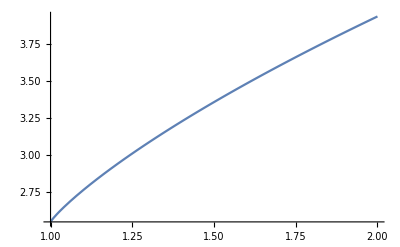

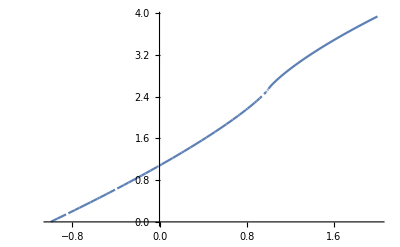

```mathematica
p1 = Plot[J1,{EE, -m g l,0}] 
p2=Plot[J2,{EE, 0,m g l}]
p3=Plot[ J3,{EE,m g l, 2 m g l}]
Show[p1,p2,p3, PlotRange->All]
```

```mathematica
mat={{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,a,b},{0,0,0,c,d}}   // Det
```

-b c+a d